```mathematica
Manipulate[
Module[{V,xN,yop,yeq,xeq,check},
V=22;
xN=x0+(yN1-y1)/(L/V);

yop[x_]:=L/V*(x-x0)+y1;

yeq[x_]:=Fit[{{2.227,1.162},{3.001,2.917},{3.339,3.783},{4.101,6.057},{4.7,8.448},{5.324,11.6}},{1,z,z^2,z^3},z]/.z->x;

check=x/.Quiet@Solve[yop[x]==yeq[x],x][[-1]];
xeq=If[check<#,check,#]&@(x/.Quiet@FindRoot[yeq[x]==yN1,{x,0}]);

Plot[{yop[x],yeq[x]},{x,2.227,xeq},PlotStyle->{{Thick,Magenta},{Thick,Orange}},PlotRange->{0,yN1+2},PlotRangePadding->None,
Frame->True,FrameLabel->{Row@{"solute/(solute-free liquid) ",Style["x",Italic], " (ppm)"},Row@{"solute/(solute-free vapor) ",Style["y",Italic]," (ppm)"}},LabelStyle->{17,Black},ImageSize->{600,370},AspectRatio->Full]
],
Grid@{{
Control[{{yN1,11.8,Row@{"outlet vapor mole ratio ",Subscript[Style["y",Italic],Row@{Style["N",Italic],"+1"}]," (ppm)"}},10,120,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{T,25,"temperature (°C)"},10,50,0.1,Appearance->"Labeled",ImageSize->Small}]
}},
Grid@{{
Control[{{P,2.5,"pressure (atm)"},1,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{L,74,"solvent flow rate (mol/h)"},50,200,1,Appearance->"Labeled",ImageSize->Small}]
}},
Grid@{{
"mole ratios (ppm):",
Control[{{y1,1.2,Row@{"inlet vapor ",Subscript[Style["y",Italic],1]}},1,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{x0,2.19,Row@{"outlet liquid ",Subscript[Style["x",Italic],0]}},0,3,0.01,Appearance->"Labeled",ImageSize->Small}]
}},
Grid@{{
Control[{{LVmin,False,Subscript[Row@{"(",Style["L",Italic],"/",Style["V",Italic],")"},"min"]},{True,False}}],
Control[{{HTS,False,"sow diagram with 5 stages"},{True,False}}],
PaneSelector[{True->Control[{{tray,1,"stage"},1,5,1,Appearance->"Labeled"}]},Dynamic@HTS]
}}
]
```

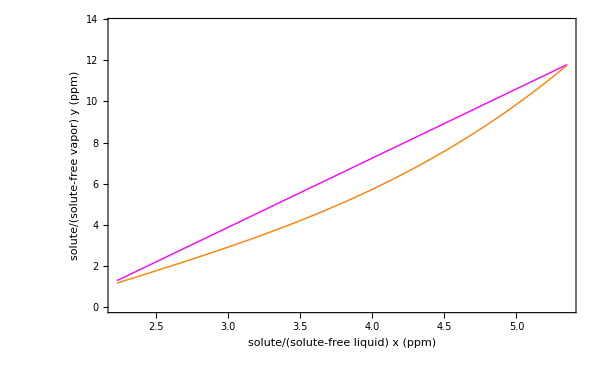

```mathematica
Module[{L,V,yN1,y1,x0,xN,yop,yeq,xeq},
L=74;V=22;
yN1=11.76;y1=1.16;x0=2.19;
xN=x0+(yN1-y1)/(L/V);

yop[x_]:=L/V*(x-x0)+y1;

yeq[x_]:=Fit[{{2.227,1.162},{3.001,2.917},{3.339,3.783},{4.101,6.057},{4.7,8.448},{5.324,11.6}},{1,z,z^2,z^3},z]/.z->x;

xeq=x/.Quiet@FindRoot[yeq[x]==yN1,{x,0}];

Plot[{yop[x],yeq[x]},{x,2.227,xeq},PlotStyle->{{Thick,Magenta},{Thick,Orange}},PlotRange->{0,yN1+2},PlotRangePadding->None,
Frame->True,FrameLabel->{Row@{"solute/(solute-free liquid) ",Style["x",Italic], " (ppm)"},Row@{"solute/(solute-free vapor) ",Style["y",Italic]," (ppm)"}},LabelStyle->{17,Black},ImageSize->{600,370},AspectRatio->Full]
]
```

```mathematica
Fit[{{2.227,1.162},{3.001,2.917},{3.339,3.783},{4.101,6.057},{4.7,8.448},{5.324,11.6}},{1,z,z^2,z^3},z]/.z->x
```

-5.26884+4.19722 x-0.871829 x^2+0.127482 x^3